## Import astro

InterpolatingFunction[…]

1.79423×10^-9

0.

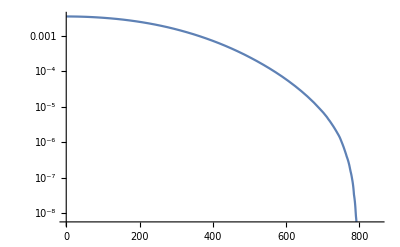

```mathematica
SetDirectory[NotebookDirectory[]];
Lgvmin=Import["gvmin_round.dat"];
ResetDirectory[];
fgvmin=Interpolation[Lgvmin,InterpolationOrder->1]
fgvmin[794]
fgvmin[795]

LogPlot[fgvmin[vmin],{vmin,0,850}]
```

## Import fion

InterpolatingFunction[…]

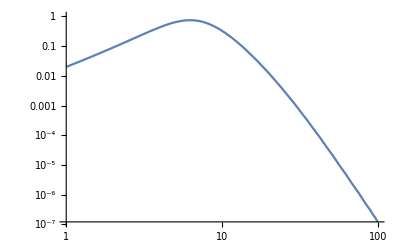

```mathematica
(*set path to form factor files*)
SetDirectory[NotebookDirectory[]<>"../Formfactor_HX"];
(*set path to form factor files*)

L1s=Import["He1s_Sch_grid.dat"];
ResetDirectory[];

f1s=Interpolation[L1s,InterpolationOrder->1]

LogLogPlot[{f1s[qx,0.02]},{qx,1,100}]
```

## Parameters

```mathematica
Params1s=Association[
wnl->2,
Inl->24.6,
fionnl->f1s
];
```

## Rate calculation: FDM = 1

σe40 is the cross section relative to 10^-40 cm^2

#### dR/dE calculation: FDM = 1

```mathematica
TdRdE[mDMMeV0_,MNGeV0_,σe40_,Params0_]:=Module[{mDMMeV=mDMMeV0,MNGeV=MNGeV0,σe40a=σe40,Params1=Params0},

wnl1=Params1[wnl];
IeV1=Params1[Inl];
fion1=Params1[fionnl];

ρ=0.3;(*GeV cm^-3*)
σe=10^-40 σe40a;(*cm^2*)
convert=4.355983 10^44;(*to convert from cm^-1 keV MeV^-3 km^-1 s to kg^-1 keV^-1 day^-1*)

meMeV=.510998928;(*MeV*)
μeMeV[mDM_]:=mDM meMeV /(meMeV +mDM);(*MeV*)

vmax=794;
ke[Eex0_]:=(2. meMeV Eex0)^0.5; (*returns momentum in keV (me MeV, Ee in eV)*)
KEmaxkeV[mDM0MeV_]:=0.5 mDM0MeV 10^3(vmax/(3 10^5))^2;
vmin[mDM0MeV_,Ee0eV_,q0keV_,I0eV_]:=Abs[(  q0keV/(2. mDM0MeV ) +(I0eV+Ee0eV)/q0keV  ) 300.];

qmaxkeV[mDM0MeV_,EekeV_,IkeV_]:=If[EekeV+IkeV<KEmaxkeV[mDM0MeV],mDM0MeV vmax/300(1+Sqrt[1- (EekeV+IkeV)/KEmaxkeV[mDM0MeV]]),0];
qminkeV[mDM0MeV_,EekeV_,IkeV_]:=If[EekeV+IkeV<KEmaxkeV[mDM0MeV],mDM0MeV vmax/300(1-Sqrt[1- (EekeV+IkeV)/KEmaxkeV[mDM0MeV]]),0];

dRdEdq[mdmMeV_,qkeV_,EekeV_,IeV_,wnl_,fion_]:=  ρ/(MNGeV mdmMeV)wnl convert 1/EekeV  σe/(8 μeMeV[mdmMeV]^2)  qkeV fgvmin[vmin[mdmMeV,10^3 EekeV,qkeV,IeV]]fion[qkeV,EekeV];

EikeV=0.001;
EfkeV=1.0;
steps=150;

TdRdE1[mdmMeV_,IeV_,wnl_,fion_]:=Table[{10.^log10EkeV,
 NIntegrate[dRdEdq[mdmMeV,qx,10^log10EkeV,IeV,wnl,fion],{qx,qminkeV[mdmMeV,10^log10EkeV,IeV/1000.],qmaxkeV[mdmMeV,10^log10EkeV,IeV/1000.]},Method->{Automatic,"SymbolicProcessing"->False}]},{log10EkeV,Log10[EikeV],Log10[EfkeV],(Log10[EfkeV]-Log10[EikeV])/steps}];

TRoutput=TdRdE1[mDMMeV,IeV1 ,wnl1,fion1]

]
```

#### dR/dE total calculation: FDM=1

```mathematica
TdRETotal[mDMMeV0_,MNGeV0_,σe40_]:=Module[{mDMMeV=mDMMeV0,MNGeV=MNGeV0,σe40a=σe40},

fσ1s=Interpolation[TdRdE[mDMMeV,MNGeV,σe40a,Params1s],InterpolationOrder->1];

Ftot[x_]:=fσ1s[x];

EikeV=0.001;
EfkeV=1.0;
steps=250;

Ttotal=Table[{10^log10ErkeV,Ftot[10^log10ErkeV]},{log10ErkeV,Log10[EikeV],Log10[EfkeV],(Log10[EfkeV]-Log10[EikeV])/steps}]
]
```

### Calculate and Plot

```mathematica
AHe=4.0023;
MNGeV=AHe .931494; (*GeV*)
σ1=1; (*10^-40cm^2 cross section*)

TR30MeV=TdRETotal[30,MNGeV,σ1];
TR300MeV=TdRETotal[300,MNGeV,σ1];
TR1000MeV=TdRETotal[1000,MNGeV,σ1];

SetDirectory[NotebookDirectory[]];
Export["dRdE_He_30MeV.dat",TR30MeV]
Export["dRdE_He_300MeV.dat",TR300MeV]
Export["dRdE_He_1000MeV.dat",TR1000MeV]
ResetDirectory[];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {25.45}. NIntegrate obtained 5.15847 and 0.000110422 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {21.1514}. NIntegrate obtained 5.11364 and 0.000160726 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {16.5669841441944}. NIntegrate obtained 5.06765 and 0.000159176 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {17.3204844942524}. NIntegrate obtained 1.32102 and 0.000673525 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {17.3383379945887}. NIntegrate obtained 1.31231 and 0.000659392 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {22.4043}. NIntegrate obtained 1.30507 and 0.000525793 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {13.98562399859313831740337263909168541431427001953125}. NIntegrate obtained 0.4203 and 0.000107843 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {26.0537}. NIntegrate obtained 0.417758 and 0.000376781 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {26.0723}. NIntegrate obtained 0.41495 and 0.000375169 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

dRdE_He_30MeV.dat

dRdE_He_300MeV.dat

dRdE_He_1000MeV.dat

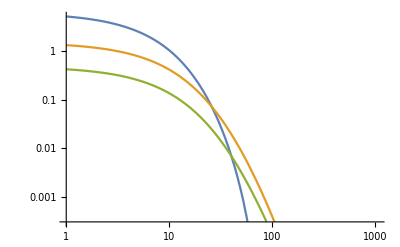

```mathematica
(*convert x-axis to eV*)
TR30MeV[[All,1]]=10^3 TR30MeV[[All,1]];
TR300MeV[[All,1]]=10^3 TR300MeV[[All,1]];
TR1000MeV[[All,1]]=10^3 TR1000MeV[[All,1]];


Show[ListLogLogPlot[{TR30MeV,TR300MeV,TR1000MeV},Joined->True,PlotRange->{{1,1070},{3 10^-4,Automatic}}]]
```

## Rate calculation: FDM = (alpha me / q)^2

σe35 is the cross section relative to 10^-37 cm^2

#### dR/dE calculation: FDM = (alpha me / q)^2

```mathematica
TdRdElightmed[mDMMeV0_,MNGeV0_,σe37_,Params0_]:=Module[{mDMMeV=mDMMeV0,MNGeV=MNGeV0,σe37a=σe37,Params1=Params0},

wnl1=Params1[wnl];
IeV1=Params1[Inl];
fion1=Params1[fionnl];

αEM=1/137.04;
ρ=0.3;(*GeV cm^-3*)
σe=10^-37 σe37a;(*cm^2*)
convert=4.355983 10^44;(*to convert from cm^-1 keV MeV^-3 km^-1 s to kg^-1 keV^-1 day^-1*)

meMeV=.510998928;(*MeV*)
mekeV=1000. meMeV;(*keV*)
μeMeV[mDM_]:=mDM meMeV /(meMeV +mDM);(*MeV*)

vmax=794;
ke[Eex0_]:=(2. meMeV Eex0)^0.5; (*returns momentum in keV (me MeV, Ee in eV)*)
KEmaxkeV[mDM0MeV_]:=0.5 mDM0MeV 10^3(vmax/(3 10^5))^2;
vmin[mDM0MeV_,Ee0eV_,q0keV_,I0eV_]:=Abs[(  q0keV/(2. mDM0MeV ) +(I0eV+Ee0eV)/q0keV  ) 300.];

qmaxkeV[mDM0MeV_,EekeV_,IkeV_]:=If[EekeV+IkeV<KEmaxkeV[mDM0MeV],mDM0MeV vmax/300(1+Sqrt[1- (EekeV+IkeV)/KEmaxkeV[mDM0MeV]]),0];
qminkeV[mDM0MeV_,EekeV_,IkeV_]:=If[EekeV+IkeV<KEmaxkeV[mDM0MeV],mDM0MeV vmax/300(1-Sqrt[1- (EekeV+IkeV)/KEmaxkeV[mDM0MeV]]),0];

FDM[qkeV_]:=(αEM mekeV/qkeV)^2;

dRdEdq[mdmMeV_,qkeV_,EekeV_,IeV_,wnl_,fion_]:=   FDM[qkeV]^2ρ/(MNGeV mdmMeV)wnl convert 1/EekeV  σe/(8 μeMeV[mdmMeV]^2)  qkeV fgvmin[vmin[mdmMeV,10^3 EekeV,qkeV,IeV]]fion[qkeV,EekeV];

EikeV=0.001;
EfkeV=1.0;
steps=150;

TdRdE1[mdmMeV_,IeV_,wnl_,fion_]:=Table[{10.^log10EkeV,
 NIntegrate[dRdEdq[mdmMeV,qx,10^log10EkeV,IeV,wnl,fion],{qx,qminkeV[mdmMeV,10^log10EkeV,IeV/1000.],qmaxkeV[mdmMeV,10^log10EkeV,IeV/1000.]},Method->{Automatic,"SymbolicProcessing"->False}]},{log10EkeV,Log10[EikeV],Log10[EfkeV],(Log10[EfkeV]-Log10[EikeV])/steps}];

TRoutput=TdRdE1[mDMMeV,IeV1 ,wnl1,fion1]

]
```

#### dR/dE total calculation: FDM = (alpha me / q)^2

```mathematica
TdRETotallightmed[mDMMeV0_,MNGeV0_,σe37_]:=Module[{mDMMeV=mDMMeV0,MNGeV=MNGeV0,σe37a=σe37},

fσ1s=Interpolation[TdRdElightmed[mDMMeV,MNGeV,σe37a,Params1s],InterpolationOrder->1];

Ftot[x_]:=fσ1s[x];

EikeV=0.001;
EfkeV=1.0;
steps=250;

Ttotal=Table[{10^log10ErkeV,Ftot[10^log10ErkeV]},{log10ErkeV,Log10[EikeV],Log10[EfkeV],(Log10[EfkeV]-Log10[EikeV])/steps}]
]
```

### Calculate and Plot

```mathematica
AHe=4.0023;
MNGeV=AHe .931494; (*GeV*)
σ1=1; (*10^-37cm^2 cross section*)

TR30MeVlightmed=TdRETotallightmed[30,MNGeV,σ1];
TR300MeVlightmed=TdRETotallightmed[300,MNGeV,σ1];
TR1000MeVlightmed=TdRETotallightmed[1000,MNGeV,σ1];

SetDirectory[NotebookDirectory[]];
Export["dRdE_He_30MeV_lightmed.dat",TR30MeVlightmed]
Export["dRdE_He_300MeV_lightmed.dat",TR300MeVlightmed]
Export["dRdE_He_1000MeV_lightmed.dat",TR1000MeVlightmed]
ResetDirectory[];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {12.927063054087}. NIntegrate obtained 8.42539 and 0.000173413 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {12.3665682185844}. NIntegrate obtained 8.30356 and 0.000224081 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {15.49622511007376690628234428004361689090728759765625}. NIntegrate obtained 8.1785 and 0.000207707 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {17.3204844942523674689027757267467677593231201171875}. NIntegrate obtained 2.26857 and 0.00172732 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {14.611504455965313553633677656762301921844482421875}. NIntegrate obtained 2.23864 and 0.00044796 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {17.35703334435988498540837099426425993442535400390625}. NIntegrate obtained 2.21248 and 0.00206734 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {13.98562399859313831740337263909168541431427001953125}. NIntegrate obtained 0.727885 and 0.000954087 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {14.00346713919021102157103086938150227069854736328125}. NIntegrate obtained 0.718915 and 0.000919405 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {14.0221513307143386128927886602468788623809814453125}. NIntegrate obtained 0.709915 and 0.000961703 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

dRdE_He_30MeV_lightmed.dat

dRdE_He_300MeV_lightmed.dat

dRdE_He_1000MeV_lightmed.dat

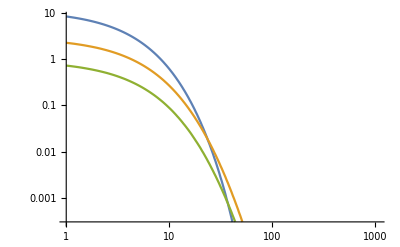

```mathematica
(*convert x-axis to eV*)
TR30MeVlightmed[[All,1]]=10^3 TR30MeVlightmed[[All,1]];
TR300MeVlightmed[[All,1]]=10^3 TR300MeVlightmed[[All,1]];
TR1000MeVlightmed[[All,1]]=10^3 TR1000MeVlightmed[[All,1]];


Show[ListLogLogPlot[{TR30MeVlightmed,TR300MeVlightmed,TR1000MeVlightmed},Joined->True,PlotRange->{{1,1070},{3 10^-4,Automatic}}]]
```